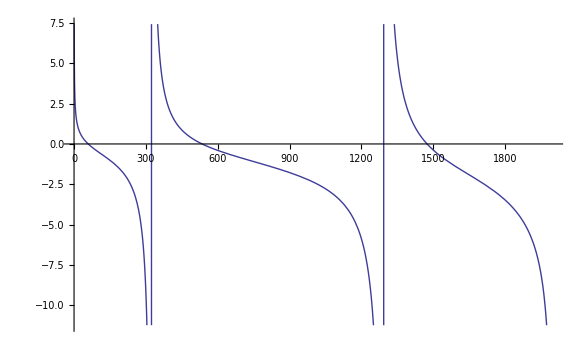

```mathematica
mw=0.186;
(*в ямі*)
mb=0.322;(*у бар'єрах*)
a=2.5;
U=2000;
ab =0.0529;
Ry =13605 (* meV *);

 k[En_]=Sqrt[(mw(En))/(Ry (ab^2))];
kap[En_]=Sqrt[(mb (U-En))/(Ry (ab^2))];


disp[En_]=Det[({{Cos[k[En]a], -ⅇ^(-kap[En] a)}, {(-k[En] Sin[k[En] a])/mw, (kap[En] ⅇ^(-kap[En] a))/mb}})];

Plot[disp[En],{En,0,2000},PlotRange->{-10^-5,10^-5}];

Plot[Cot[k[En]a]-k[En] mb/(kap[En]mw),{En,0,2000}]
```

```mathematica
FindRoot[disp[En],{En,500}]
FindRoot[disp[En],{En,1500}]
```

{En→534.749}

{En→1474.23}